# Ex 1:

Direct Integration

```mathematica
f[z_]=1/(2π I)Exp[z t]/(z^2(z^2+2z+2));

z=3Cos[θ]+I 3Sin[θ];
```

```mathematica
DI=Integrate[f[z] D[z,θ],{θ,0,2π},Assumptions->t>0]
```

1/2 (-1+t+ⅇ^-t Cos[t])

Residue Theorem

```mathematica
Solve[k^2(k^2+2k+2)==0]
```

{{k→-1-ⅈ},{k→-1+ⅈ},{k→0},{k→0}}

```mathematica
res1=Residue[f[k],{k,-1-ⅈ}];
res2=Residue[f[k],{k,-1+ⅈ}];
res3=Residue[f[k],{k,0}];
```

```mathematica
Int=2π I(res1+res2+res3+res3)
```

2 ⅈ π (-(ⅈ ⅇ^((-1-ⅈ) t))/(8 π)-(ⅈ ⅇ^((-1+ⅈ) t))/(8 π)-(ⅈ (-1+t))/(2 π))

```mathematica
RT=FullSimplify[Int]
```

-1+t+1/2 ⅇ^-t Cos[t]

Plots

```mathematica
u[{x_,y_}]=FullSimplify[ComplexExpand[Re[f[x+I y]]]];
v[{x_,y_}]=FullSimplify[ComplexExpand[Im[f[x+I y]]]];
ϕ[{x_,y_}]={u[{x,y}],v[{x,y}]};
ϕ̄[{x_,y_}]={u[{x,y}],-v[{x,y}]};
SuperStar[ϕ][{x_,y_}]={v[{x,y}],u[{x,y}]};
Subscript[x, z0_,R_][t_]:=Re[z0]+R Cos[t]
Subscript[y, z0_,R_][t_]:=Im[z0]+R Sin[t]
Subscript[Z, z0_,R_][t_]:=Subscript[x, z0,R][t]+I Subscript[y, z0,R][t]
Subscript[r, z0_,R_][t_]:={Subscript[x, z0,R][t], Subscript[y, z0,R][t]}
```

True

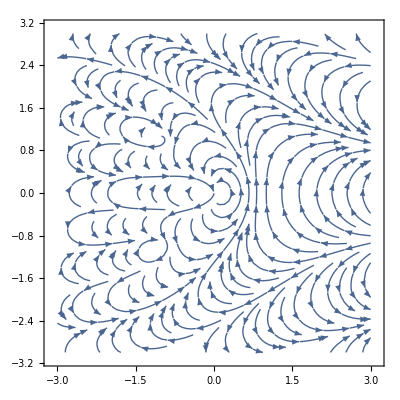

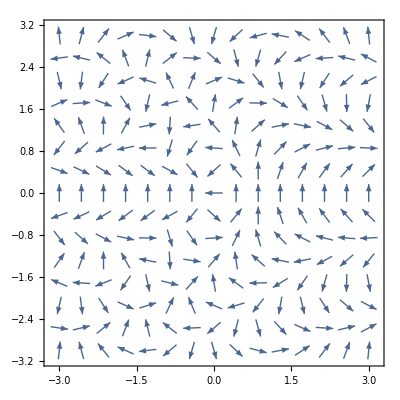

```mathematica
t>0
StreamPlot[ϕ̄[{x,y}],{x,-3,3},{y,-3,3}]
VectorPlot[ϕ̄[{x,y}],{x,-3,3},{y,-3,3}, VectorScale->{0.04,0.7,None}]
```

# Ex 2:

I need to show that: ∫_0^(2π) 1/(a+bSin(θ))ⅆθ=(2π)/(√(a^2-b^2)) using residue theorem and sinθ = (e^iθ- e^-iθ)/(2 i)=(z-z^-1)/(2i) and dz=ie^iθ dθ=izdθ 
which means that dθ=dz/iz

```mathematica
f[z_]=(1/(I z))/(a+b((z-z^-1)/(2 I)))
```

-ⅈ/(z (a-1/2 ⅈ b (-1/z+z)))

```mathematica
Solve[z (a-1/2 ⅈ b (-1/z+z))==0,z]
```

{{z→(-ⅈ a-ⅈ √(a^2-b^2))/b},{z→(-ⅈ a+ⅈ √(a^2-b^2))/b}}

```mathematica
res1=Residue[f[z],{z,(-ⅈ a-ⅈ √(a^2-b^2))/b}]
res2=Residue[f[z],{z,(-ⅈ a+ⅈ √(a^2-b^2))/b}]
```

ⅈ/(√(a^2-b^2))

-ⅈ/(√(a^2-b^2))

```mathematica
sol=2π I(res2)
```

(2 π)/(√(a^2-b^2))

There are 2 residue points, we took a circle with a radius 1 and the point of res2 is closer to (0,0) than the other one.